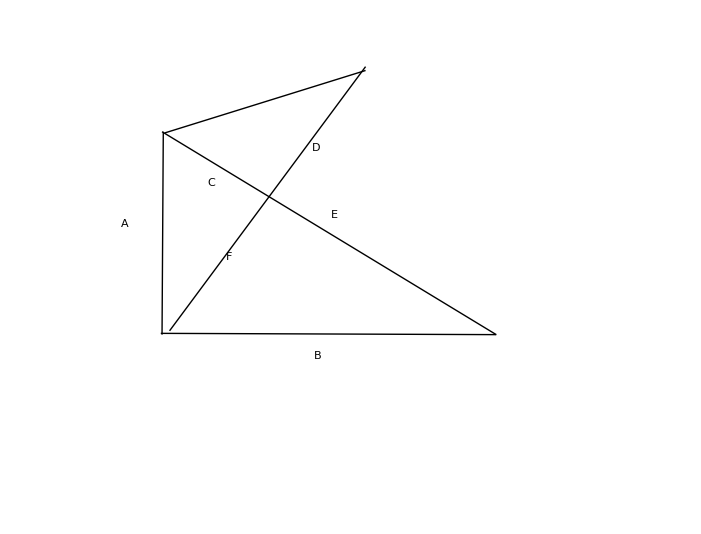

```mathematica
Clear["Global`*"]

h=√(a^2+b^2);
θ=ArcTan[a/b];
e=b Cos[θ];
f=b*Sin[θ];
d=b-f;
c=h-e;
a/b==c/d;



a/b==c/d
a/b==(h-e)/d
a/b==(h-e)/(b-f)
a/b==(√(a^2+b^2)-e)/(b-f)
a/b==(√(a^2+b^2)-b Cos[θ])/(b-f)
a/b==(√(a^2+b^2)-b Cos[θ])/(b-b*Sin[θ])
a/b==(√(a^2+b^2)-b Cos[ArcTan[a/b]])/(b-b*Sin[ArcTan[a/b]])
a/b==(√(a^2+b^2)-b/(√(1+a^2/b^2)))/(b-a/(√(1+a^2/b^2)))
a(b-a/(√(1+a^2/b^2)))==b(√(a^2+b^2)-b/(√(1+a^2/b^2)))
a b-a^2/(√(1+a^2/b^2))==b √(a^2+b^2)-b^2/(√(1+a^2/b^2))
a b √(1+a^2/b^2)-a^2==b √(a^2+b^2)√(1+a^2/b^2)-b^2
(*SIDE NOTE*)
√(a^2+b^2)√(1+a^2/b^2)
√((a^2+b^2)(1+a^2/b^2))
√(a^2+a^4/b^2+b^2+a^2)
√(a^4/b^2+2 a^2 b^2/b^2+b^4/b^2)
√((a^4+2 a^2 b^2+b^4)/b^2)
√(((a^2+b^2)^2)/b^2)
(*End of side note*)

a b √(1+a^2/b^2)-a^2==b √(a^2+b^2)√(1+a^2/b^2)-b^2
a b √(1+a^2/b^2)-a^2==b √(((a^2+b^2)^2)/b^2)-b^2
a b √(1+a^2/b^2)-a^2==b(a^2+b^2)/b-b^2
a b √(1+a^2/b^2)-a^2==(a^2+b^2)-b^2
a b √(1+a^2/b^2)==a^2+a^2+b^2-b^2
a b √(1+a^2/b^2)==2 a^2
b √(1+a^2/b^2)==2a
b^2(√(1+a^2/b^2))^2==(2a)^2
b^2(1+a^2/b^2)==4 a^2
b^2+(b^2 a^2)/b^2==4 a^2
b^2+a^2==4 a^2
b^2==4 a^2-a^2
b^2==3 a^2
b==√(3 a^2)
b==√3 a
```

```mathematica
√3. 3
```

5.19615

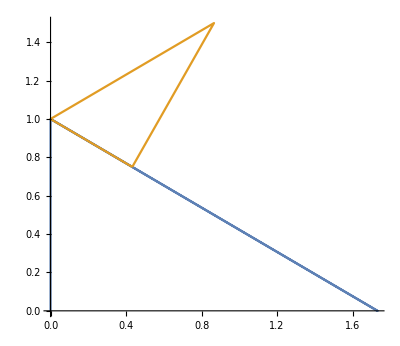

```mathematica
b=√3;
mag=Norm[p1-p3];
ϕ=ArcTan[e/f];
p1={0,0};
p2={0,1};
p3={√3,0};
p4={mag*Cos[ϕ],mag*Sin[ϕ]};
p5={f*Cos[ϕ],f*Sin[ϕ]};

ListPlot[{{p1,p2,p3,p2},{p5,p2,p4,p5}},Joined->True,AspectRatio->Automatic]
```

```mathematica
v1=p4-p1
v2=p3-p2
ArcCos[(v1.v2)/(Norm[v1]*Norm[v2])]*180/π
```

{(√3)/2,3/2}

{√3,-1}

90

```mathematica
b/a==(√(a^2+b^2)-b Cos[ArcTan[a/b]])/(b-b*Sin[ArcTan[a/b]])
```

b/a==(-b/(√(1+a^2/b^2))+√(a^2+b^2))/(-a/(√(1+a^2/b^2))+b)

```mathematica
√(a^2+b^2)-b Cos[ArcTan[a/b]]
```

-b/(√(1+a^2/b^2))+√(a^2+b^2)

```mathematica
√(a^2+b^2)√(1+a^2/b^2)
√((a^2+b^2)(1+a^2/b^2))
√((a^2+b^2)(1+a^2/b^2))
√(a^2+a^4/b^2+b^2+a^2)
√(a^4/b^2+2 a^2 b^2/b^2+b^4/b^2)
√((a^4+2 a^2 b^2+b^4)/b^2)
√(((a^2+b^2)^2)/b^2)
```

√(1+a^2/b^2) √(a^2+b^2)

√((1+a^2/b^2) (a^2+b^2))

√((1+a^2/b^2) (a^2+b^2))

√(2 a^2+a^4/b^2+b^2)

√(2 a^2+a^4/b^2+b^2)

√(((a^2+b^2)^2)/b^2)

a/(√(1+a^2/b^2) b)

```mathematica
a/b==(√(a^2+b^2)-b 1/(√(1+a^2/b^2)))/(b-b*a/(√(1+a^2/b^2) b))
```

```mathematica
Cos[ArcTan[a/b]]==1/(√(1+a^2/b^2))
Sin[ArcTan[a/b]]==a/(√(1+a^2/b^2) b)
```

True

a/(√(1+a^2/b^2) b)